```mathematica
markers=Import[NotebookDirectory[]<>"output_markers.dat"];
xbeammg=Import[NotebookDirectory[]<>"output_xbeam_mg_pos1.dat"];
xbeamcr=Import[NotebookDirectory[]<>"output_xbeam_cr_pos1.dat"]; 
xbeammg2=Import[NotebookDirectory[]<>"output_xbeam_mg_pos2.dat"];
xbeamcr2=Import[NotebookDirectory[]<>"output_xbeam_cr_pos2.dat"];
```

```mathematica
plotmg = ListPlot[{ xbeammg}, Joined->True, AspectRatio->.4,  Filling->None, PlotRange->All, PlotStyle->Directive[Red,Opacity[.15]],FillingStyle->Red, Ticks->Automatic];
plotcr = ListPlot[{ xbeamcr}, Joined->True, AspectRatio->.4,  Filling->None, PlotRange->All, PlotStyle->Directive[Blue,Opacity[.15]], FillingStyle->Green, Ticks->Automatic];

plotmg2 = ListPlot[{ xbeammg2}, Joined->True, AspectRatio->.4,  Filling->None, PlotRange->All, PlotStyle->Directive[Red,Opacity[.15]],FillingStyle->Red, Ticks->Automatic];
plotcr2 = ListPlot[{ xbeamcr2}, Joined->True, AspectRatio->.4,  Filling->None, PlotRange->All, PlotStyle->Directive[Blue,Opacity[.15]], FillingStyle->Green, Ticks->Automatic];

markersplot= ListPlot[{ markers}, Joined->True, AspectRatio->.4,  Filling->None, PlotRange->{-30,30}, PlotStyle->RGBColor[.7,.7,.7], Ticks->Automatic];//Quiet
```

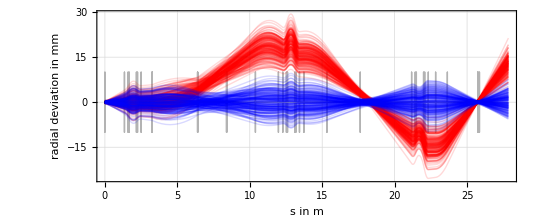

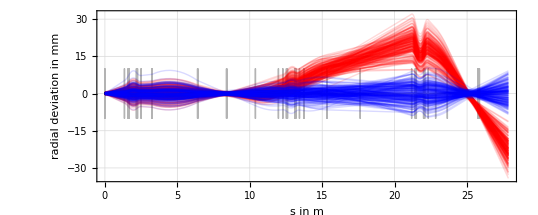

```mathematica
Show[markersplot, plotmg, plotcr, PlotRange->{All,All},Frame->True,  FrameLabel->{"s in m","radial deviation in mm"}, FrameTicks->{Automatic,Automatic,{{4.8,"analyzing-MAGNET", {.4,0}, Dashed},{12.83,"ESA - QPT - ESA", {.4,0}, Dashed},{23.5,"switching-MAGNET                      ", {.4,0}, Dashed},{25.7,"           DETECTOR", {.4,0}, Dashed}},Automatic}, GridLines->Automatic, GridLinesStyle->Opacity[.3]]

Show[markersplot, plotmg2, plotcr2, PlotRange->{All,All},Frame->True,  FrameLabel->{"s in m","radial deviation in mm"}, FrameTicks->{Automatic,Automatic,{{4.8,"analyzing-MAGNET", {.4,0}, Dashed},{12.83,"ESA - QPT - ESA", {.4,0}, Dashed},{23.5,"switching-MAGNET                      ", {.4,0}, Dashed},{25.7,"           DETECTOR", {.4,0}, Dashed}},Automatic}, GridLines->Automatic, GridLinesStyle->Opacity[.3]]
```